```mathematica
(* Pivot Function *)
pivot[m_,iStar_, jStar_] :=(
(* Create copy of matrix  and get dimensions *)
mm=m;
rows=Dimensions[m][[1]];
cols=Dimensions[m][[2]];
(* Begin Pivoting *)
mm[[1,jStar] ]=m[[iStar,cols]]; 
mm[[iStar,cols]]=m[[1,jStar]];
For[row=2, row≤rows, row++,
For[col=1,col<cols,col++,
{
(* P *)
If[row==iStar && col==jStar,
mm[[row,col]]=1/m[[iStar,jStar]]],
(* Q *)
If[row==iStar && col ≠ jStar,
mm[[row,col]]=-m[[row,col]]/m[[iStar, jStar]]],
(* R *)
If[row≠iStar && col== jStar,
mm[[row,col]]=m[[row,col]]/m[[iStar, jStar]]],
(* S *)
If[row≠iStar && col ≠ jStar,
mm[[row,col]]=m[[row,col]]-m[[iStar,col]]m[[row,jStar]]/m[[iStar,jStar]]]
}
]
];
Return[mm];
)
```

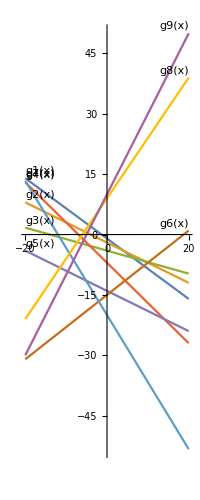

```mathematica
(* Define Boundary Functions *)
g1[x_,y_]:=-3x-4y;
g2[x_,y_]:=x+2y;
g3[x_,y_]:=-2x-7y;
g4[x_,y_]:=2x+2y;
g5[x_,y_]:=x+2y;
g6[x_,y_]:=-4x+5y;
g7[x_,y_]:=5x+3y;
g8[x_,y_]:=-3x+2y;
g9[x_,y_]:=-2x+y;

b1=4;b2=-4;b3=28;b4=-14;b5=-28;b6=-75;b7=-60;b8=18;b9=10;

g1[x_]:=y/.Solve[g1[x,y]==b1,{y}][[1,1]]
g2[x_]:=y/.Solve[g2[x,y]==b2,{y}][[1,1]]
g3[x_]:=y/.Solve[g3[x,y]==b3,{y}][[1,1]]
g4[x_]:=y/.Solve[g4[x,y]==b4,{y}][[1,1]]
g5[x_]:=y/.Solve[g5[x,y]==b5,{y}][[1,1]]
g6[x_]:=y/.Solve[g6[x,y]==b6,{y}][[1,1]]
g7[x_]:=y/.Solve[g7[x,y]==b7,{y}][[1,1]]
g8[x_]:=y/.Solve[g8[x,y]==b8,{y}][[1,1]]
g9[x_]:=y/.Solve[g9[x,y]==b9,{y}][[1,1]]

Plot[{g1[x],g2[x],g3[x],g4[x],g5[x],g6[x],g7[x],g8[x],g9[x]},{x,-20,20},{AspectRatio->Automatic},PlotLabels->Placed[Automatic,Above]]
```

```mathematica
(* Defining all constraints with ≤ *)
(*  3x + 4y ≤ -04 *)
(*   x + 2y ≤ -04 *)
(*  2x + 7y ≤ -28 *)
(*  2x + 2y ≤ -14 *)
(* - x - 2y ≤  28 *)
(*  4x - 5y ≤  75 *)
(* -5x - 3y ≤  60 *)
(* -3x + 2y ≤  18 *)
(* -2x +  y ≤  10 *)

(* Adding in and solving for slack variables *)
(* s1 = -04 - 3x - 4y *)
(* s2 = -04 - 1x - 2y *)
(* s3 = -28 - 2x - 7y *)
(* s4 = -14 - 2x - 2y *)
(* s5 =  28 + 1x + 2y *)
(* s6 =  75 - 4x + 5y *)
(* s7 =  60 + 5x + 3y *)
(* s8 =  18 + 3x - 2y *)
(* s9 =  10 + 2x - 1y *)

(* Substituting x1= v1-v2,x2=v2-v4 into tableau*)
(* Objective function becomes: 10v1 - 10v2 + 6v3 - 6v4 - 12 *)

(* Create vector of variables for Bland's Rule *)
blandVector = {v1,v2,v3,v4,s1,s2,s3,s4,s5,s6,s7,s8,s9}

(* Defining t0 *)
m0={v1,v2,v3,v4,1,""};
m1 ={-3,3,-4,4,-04,s1};
m2 ={-1,1,-2,2,-04,s2};
m3 ={-2,2,-7,7,-28,s3};
m4 ={-2,2,-2,2,-14,s4};
m5 ={ 1,-1,2,-2,28,s5};
m6 ={-4,4,5,-5,75,s6};
m7 ={5,-5,3,-3,60,s7};
m8 ={3,-3,-2,2,18,s8};
m9 ={2,-2,-1,1,10,s9};
mobj={10,-10,6,-6,-12,z->min};
t0={m0,m1,m2,m3,m4,m5,m6,m7,m8,m9,mobj};
Print["t0 = ",MatrixForm[t0]]
```